```mathematica
Quit[]
```

## Declarations

```mathematica
<<FractionalIteration`
```

```mathematica
Series[A[a,x,1],{x,0,3}]//Inv
```

(x-1)/Log[a]-(x-1)^2/(2 Log[a])+(x-1)^3/(3 Log[a])+O[x-1]^4

```mathematica
Inv[Series[A[E,x,1],{x,0,3}]]
```

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3+O[x-1]^4

```mathematica
a^p[1]^=a
```

a

```mathematica
a^p[1]^=a;
A[a,1][x_]:=a^x;
A[a,n_][x_]:=p[n]+FI[A[a,n-1] ,n,x,p[n-1]];
```

```mathematica
A[a,2][x]=p[2]+FI[A[a,1],n,x,p[1]]/. a^p[1]->a
```

{False,Universal,Symbolic}

(a Log[a])^n (x-p[1])+1/2 a (∑_(k_1=0)^(-1+n) (a Log[a])^(-2+2 n-k_1)) Log[a]^2 (x-p[1])^2+1/6 (a (∑_(k_1=0)^(-1+n) (a Log[a])^(-3+3 n-2 k_1)) Log[a]^3+3 a^2 (∑_(k_1=0)^(-1+n) ∑_(k_2=0)^(-2+n-k_1) (a Log[a])^(-5+3 n-k_2-2 k_1)) Log[a]^4) (x-p[1])^3+1/24 (a (∑_(k_1=0)^(-1+n) (a Log[a])^(-4+4 n-3 k_1)) Log[a]^4+6 a^2 (∑_(k_1=0)^(-1+n) ∑_(k_2=0)^(-2+n-k_1) (a Log[a])^(-6+4 n-k_2-3 k_1)) Log[a]^5+4 a^2 (∑_(k_1=0)^(-1+n) ∑_(k_2=0)^(-2+n-k_1) (a Log[a])^(-7+4 n-2 k_2-3 k_1)) Log[a]^5+3 a^3 (∑_(k_1=0)^(-1+n) ∑_(k_2=0)^(-2+n-k_1) ∑_(k_3=0)^(-2+n-k_1) (a Log[a])^(-8+4 n-k_2-k_3-3 k_1)) Log[a]^6+12 a^3 (∑_(k_1=0)^(-1+n) ∑_(k_2=0)^(-2+n-k_1) ∑_(k_3=0)^(-3+n-k_2-k_1) (a Log[a])^(-9+4 n-k_3-2 k_2-3 k_1)) Log[a]^6) (x-p[1])^4+p[1]+p[2]

```mathematica
D[A[a,2][x],x]
```

A[a,2]'[x]

```mathematica
Derivative[0,1,0][Ackermann][a,x,2] //InputForm
```

Derivative[0, 1, 0][Ackermann][a, x, 2]

```mathematica
Series[A[a,2][x],{x,0,3}]
```

1+Ackermann^(0,1,0)[a,0,2] x+1/2 Ackermann^(0,2,0)[a,0,2] x^2+1/6 Ackermann^(0,3,0)[a,0,2] x^3+O[x]^4

```mathematica
Inv[Series[A[a,2][x],{x,0,3}]]
```

(x-1)/(Ackermann^(0,1,0)[a,0,2])-(Ackermann^(0,2,0)[a,0,2] (x-1)^2)/(2 (Ackermann^(0,1,0)[a,0,2])^3)+((((Ackermann^(0,2,0)[a,0,2])^2)/(2 (Ackermann^(0,1,0)[a,0,2])^2)-(Ackermann^(0,3,0)[a,0,2])/(6 Ackermann^(0,1,0)[a,0,2])) (x-1)^3)/((Ackermann^(0,1,0)[a,0,2])^3)+O[x-1]^4

```mathematica
InvA[a_,b_,n_]:=Inv[Series[A[a,n][b],{x,0,3}]];
(*InvA[a_,n_][x_]:=InvA[a,x,n];*)
```

```mathematica
FixedPoint[InvA[E,#,1]&,1.0+I]
```

General::ivar: 1.+1. ⅈ is not a valid variable.

```mathematica
InvA[E,#,1]&[1.0+I]
```

General::ivar: 1.+1. ⅈ is not a valid variable.

InverseSeries[Series[1.46869+2.28736 ⅈ,{1.+1. ⅈ,0,3}]]

```mathematica
InvA[E,#,1]&[a]
```

InvA[ⅇ,a,1]

```mathematica
InvA[E,1]
```

InvA[ⅇ,1]

```mathematica
(#/3.0)&[x]
```

0.333333 x

```mathematica
FixedPoint[(#/3.0)&,1.0+I]
```

General::munfl: 0.333333 (5.41891×10^-308+5.41891×10^-308 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

0.+0. ⅈ

## Stuff

```mathematica
p[n_Integer/;n>1]:=A[x,-∞,n]
```

```mathematica
p[0]
```

p[0]

```mathematica
A[x_,y,2]:=A[x,-∞,1]+FI[]
```

```mathematica
A[a,1][z]
```

a^z

```mathematica
A[a_,b_,n_]:=Ackermann[a,b,n]
```

```mathematica
A[a_,n_][b_]:=Ackermann[a,b,n]
```

```mathematica
Format[Ackermann[a_,b_,n_]]:= HoldForm[a Superscript["↑",n]b];
```

```mathematica
Format[Ackermann[a_,n_][b_]]:= HoldForm[a Superscript["↑",n]b];

A[a,b,n]
```

a ↑^n b

```mathematica
A[a,n][b]
```

a ↑^n b

```mathematica
FI[A[a,1],n,z,p[2],2]
```

{False,Universal,Symbolic}

x ↑^2 (-∞)+1/2 a^(x ↑^2 (-∞)) (z-x ↑^2 (-∞))^2 (∑_(k_1=0)^(-1+n) (a^(x ↑^2 (-∞)) Log[a])^(-2+2 n-k_1)) Log[a]^2+(z-x ↑^2 (-∞)) (a^(x ↑^2 (-∞)) Log[a])^n

```mathematica
A[a,1][-∞]
```

Infinity::indet: Indeterminate expression a^(-∞) encountered.

Indeterminate

## Quit

```mathematica
Quit[]
```

## Work

```mathematica
<<FractionalIteration`
```

```mathematica
FI[f,n,x,p,2]
```

{False,Universal,Symbolic}

p+(-p+x) f'[p]^n+1/2 (-p+x)^2 (∑_(k_1=0)^(-1+n) f'[p]^(-2+2 n-k_1)) f''[p]

```mathematica
b=Exp[1];
branch=0;
(*f[z_]:=N[Log[b,z]+2 Pi I branch]*)
f[z_]:=N[Log[z]]
p=FixedPoint[f,1.0+I]
```

0.318132+1.33724 ⅈ

```mathematica
p=FixedPoint[Log,1.0+I]
```

0.318132+1.33724 ⅈ

```mathematica
FractionalIteration[f,n,z,FixedPoint[Log,1.0+I],2] /.HoldForm->Identity /.z->1
```

{True,Universal,Symbolic}

(0.318132+1.33724 ⅈ)+(0.681868-1.33724 ⅈ) (0.168376-0.707754 ⅈ)^n+(7.23683×10^-35-1.63651×10^-32 ⅈ) (1.56735×10^15-6.58819×10^15 ⅈ)^n (9.30859×10^15)^(2.-1. n) (-1.+(0.168376-0.707754 ⅈ)^n)

```mathematica
p+(-p+z) f'[p]^n+((-p+z)^2 f'[p]^(-1+n) (-1+f'[p]^n) f''[p])/(2 (-1+f'[p])) /.z->1
```

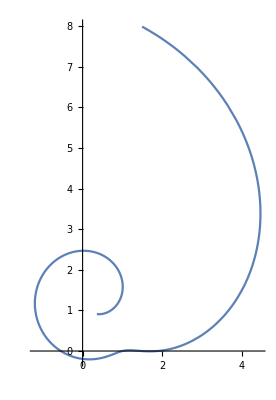

```mathematica
ParametricPlot[{Re[(0.318131505204764+1.3372357014306895 ⅈ)+(0.681868494795236-1.3372357014306895 ⅈ) (0.16837637908722283-0.7077541887847276 ⅈ)^n+(0.4158118104563885+0.3538770943923638 ⅈ) (0.16837637908722283-0.7077541887847276 ⅈ)^(-1+n) (-1+(0.16837637908722283-0.7077541887847276 ⅈ)^n)],Im[(0.318131505204764+1.3372357014306895 ⅈ)+(0.681868494795236-1.3372357014306895 ⅈ) (0.16837637908722283-0.7077541887847276 ⅈ)^n+(0.4158118104563885+0.3538770943923638 ⅈ) (0.16837637908722283-0.7077541887847276 ⅈ)^(-1+n) (-1+(0.16837637908722283-0.7077541887847276 ⅈ)^n)]},{n,-2,5}]
```